### Константы

```mathematica
ME=10^10;ν=0.3;λ=(ν ME)/((1+ν)(1-2ν));μ=ME/(2(1+ν)); dz=-0.1;U0=0.1;
b=0.6;a=1; p0=P0=100000000;
bx=1;by=1;
```

### [i,k] — Перемещения в направлении i, от нагрузки, равномерно распределённой в направлении k, по прямоугольной области(a на b) в виде скомпилированных функций

```mathematica
U[1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[2,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
-(p0 x3 (λ+μ))/(8 π μ (λ+2 μ))*(Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])
],
CompilationTarget->"C"
];
```

```mathematica
U[3,3] =  Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];p0/(8 π μ (λ+2 μ))*(2 x3 μ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])+(λ+3 μ) (x2 (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)])+x1 (Log[x2+√(x1^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)])+(-b+x2) (-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)])+(-a+x1) (-Log[x2+√((-a+x1)^2+x2^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)])))
],
CompilationTarget->"C"
];
```

### [i,j,k] — Напряжения i,j от нагрузки равномерно распределённой в направлении k, по прямоугольной области (a на b) в виде скомпилированных функций

```mathematica
σ[1,1,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ))*(-1/(√(x1^2+x2^2+x3^2))+1/(√((-a+x1)^2+x2^2+x3^2))+1/(√(x1^2+(-b+x2)^2+x3^2))-1/(√((-a+x1)^2+(-b+x2)^2+x3^2)))
],
CompilationTarget->"C"
];
```

```mathematica
σ[1,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ)) ((λ+μ)*((x2 x3^2)/((x1^2+x3^2) √(x1^2+x2^2+x3^2))-(x2 x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-((-b+x2) x3^2)/((x1^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-b+x2) x3^2)/(((-a+x1)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x2+√(x1^2+x2^2+x3^2)]-Log[x2+√((-a+x1)^2+x2^2+x3^2)]-Log[-b+x2+√(x1^2+(-b+x2)^2+x3^2)]+Log[-b+x2+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,2,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*(x3 (λ+μ) ((x1 x2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 (-b+x2))/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) (-b+x2))/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+λ (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[2,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
p0/(4 π (λ+2 μ))*((λ+μ) ((x1 x3^2)/((x2^2+x3^2) √(x1^2+x2^2+x3^2))-((-a+x1) x3^2)/((x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))-(x1 x3^2)/(((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((-a+x1) x3^2)/(((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+μ (Log[x1+√(x1^2+x2^2+x3^2)]-Log[-a+x1+√((-a+x1)^2+x2^2+x3^2)]-Log[x1+√(x1^2+(-b+x2)^2+x3^2)]+Log[-a+x1+√((-a+x1)^2+(-b+x2)^2+x3^2)]))
],
CompilationTarget->"C"
];
```

```mathematica
σ[3,3,3] = Compile[{{x1,_Real},{a,_Real},{x2,_Real},{b,_Real},{x03,_Real},{p0,_Real},{λ,_Real},{μ,_Real}},
Module[{x3=x03},
If[x3>-0.000001*a&&x3≤0.,x3=-0.000001*a,
If[x3<0.000001*a&&x3>0.,x3=0.000001*a]];
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))])

],
CompilationTarget->"C"
];
```

```mathematica
σ1[x1_,x2_,x3_,a_,b_] =
(p0 x3 (λ+μ))/(4 π (λ+2 μ)) (-(x1 x2 (x1^2+x2^2+2 x3^2))/((x1^2+x3^2) (x2^2+x3^2) √(x1^2+x2^2+x3^2))+((-a+x1) x2 ((-a+x1)^2+x2^2+2 x3^2))/(((-a+x1)^2+x3^2) (x2^2+x3^2) √((-a+x1)^2+x2^2+x3^2))+(x1 (-b+x2) (x1^2+(-b+x2)^2+2 x3^2))/((x1^2+x3^2) ((-b+x2)^2+x3^2) √(x1^2+(-b+x2)^2+x3^2))+((a-x1) (-b+x2) ((-a+x1)^2+(-b+x2)^2+2 x3^2))/(((-a+x1)^2+x3^2) ((-b+x2)^2+x3^2) √((-a+x1)^2+(-b+x2)^2+x3^2)))+p0/(4 π) (-ArcTan[(x1 x2)/(x3 √(x1^2+x2^2+x3^2))]+ArcTan[((-a+x1) x2)/(x3 √((-a+x1)^2+x2^2+x3^2))]+ArcTan[(x1 (-b+x2))/(x3 √(x1^2+(-b+x2)^2+x3^2))]-ArcTan[((-a+x1) (-b+x2))/(x3 √((-a+x1)^2+(-b+x2)^2+x3^2))]);
```

## 1) Графики

### Графики напряжений

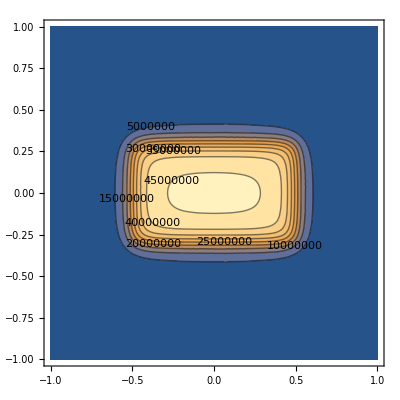

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

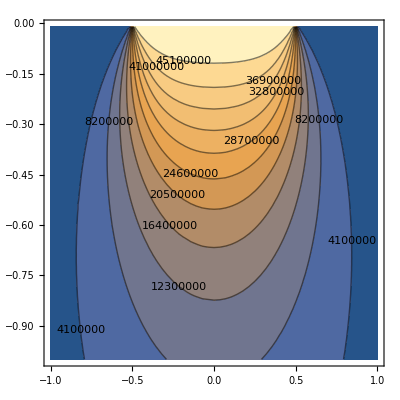

```mathematica
Print[ContourPlot[σ[3,3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->11,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

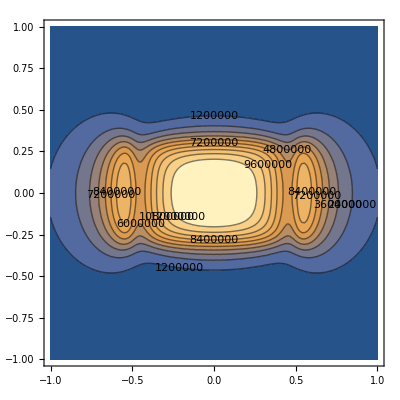

```mathematica
Print[ContourPlot[σ[1,1,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

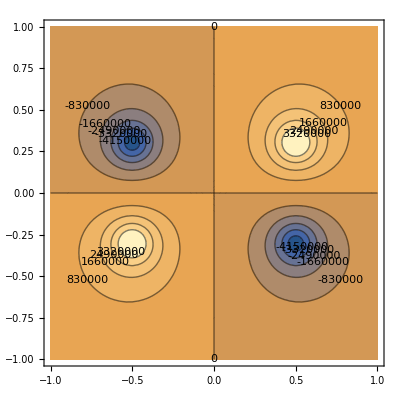

```mathematica
Print[ContourPlot[σ[1,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

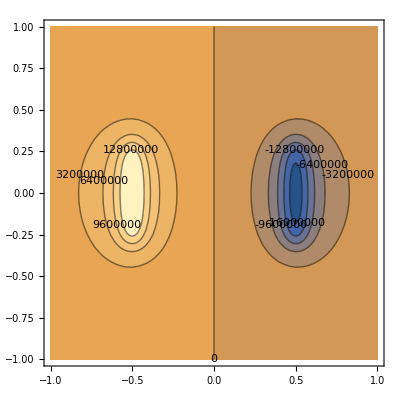

```mathematica
Print[ContourPlot[σ[1,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

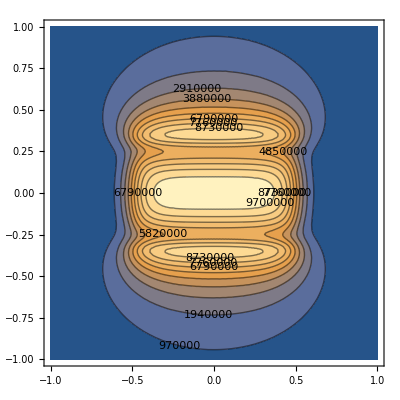

```mathematica
Print[ContourPlot[σ[2,2,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

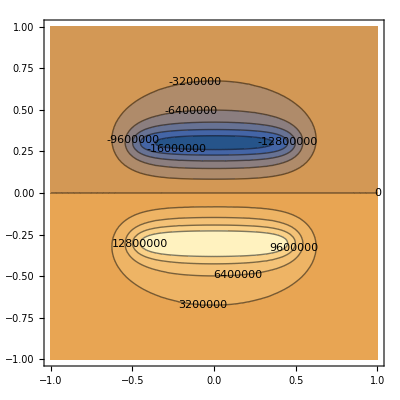

```mathematica
Print[ContourPlot[σ[2,3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

### Графики перемещений

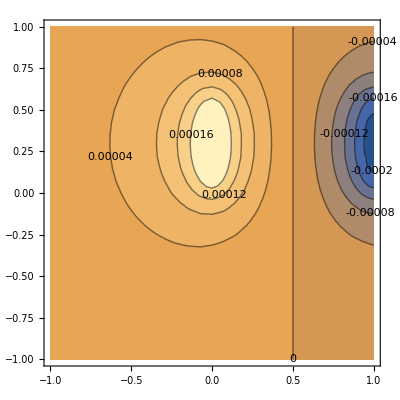

```mathematica
Print[ContourPlot[U[1,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

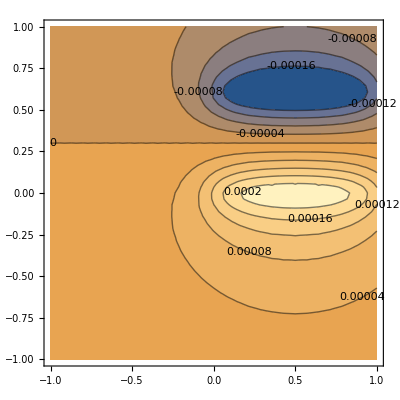

```mathematica
Print[ContourPlot[U[2,3][x,a,y,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

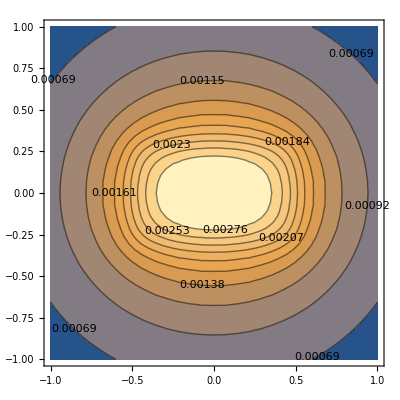

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,y+b/2,b,dz,P0,λ,μ] ,{x,-bx,bx},{y,-by,by},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

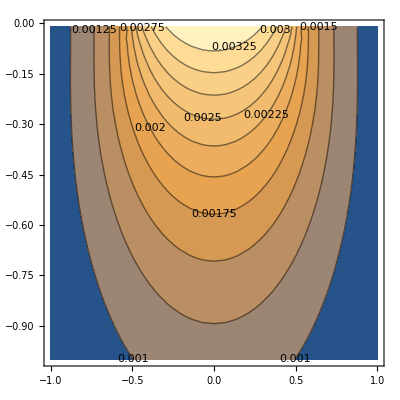

```mathematica
Print[ContourPlot[U[3,3][x+a/2,a,b/2,b,z,P0,λ,μ] ,{x,-bx,bx},{z,-by,-by/100},Contours->10,ContourLabels->True,AspectRatio->by/bx,PlotRange->All]];
```

## 2) Граничная задача для вдавливания плоского эллиптического штампа

#### Инициализация и графики поверхностного распределения и дискретизации функции поверхностного распределения

```mathematica
Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,Re[P0 √(1-(x/a)^2-(y/b)^2)],0];
Displacement[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,U0,0];
(*Pressure[x_,y_,a_,b_,p0_]=If[(x/a)^2+(y/b)^2≤1,P0,0];*)
s=1.5*a;(*размер расчетной области*)
(*Установить h = 3a/19 для n = 20*)
h= 3a /9;(*размер ГЭ*)
n=2 s/h+1(*number of elementary units*)
(*array of X-coordinates*)
X=Table[xh,{xh,-s,s,h}];
Y=Table[yh,{yh,-s,s,h}];
Plot3D[Pressure[x,y,a,b,P0],{x,-s,s},{y,-s,s},AxesLabel->Automatic,PlotRange->All]
```

10.

-Graphics3D-

```mathematica
DisplacementTab=Table[Displacement[X[[xi]],Y[[yj]],a,b,P0],{xi,1,n},{yj,1,n}];
PressureTab=Table[Pressure[X[[xi]],Y[[yj]],a,b,P0]//N,{xi,1,n},{yj,1,n}];
ListPlot3D[DisplacementTab,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
BoundaryElements=Table[{X[[xi]],Y[[yj]],DisplacementTab[[xi,yj]]},{xi,1,n},{yj,1,n}];
```

### Получение решения последовательно

```mathematica
Pk1 = Table[Subscript[p, k],{k,1,n^2}];
(*PotV[xj_,yj_] =Sum[σ1[X[[m]]-xj,Y[[o]]-yj,-0.001,h,h]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}];
FPT=Flatten[PressureTab];*)
```

```mathematica
(*Equationq=Flatten[Table[PotV[X[[i]],Y[[j]]]==PressureTab[[i,j]],{i,1,n},{j,1,n}]];*)
Equationq=Flatten[Table[Sum[U[3,3][X[[m]]-X[[i]],h,Y[[o]]-Y[[j]],h,0.01,p0,λ,μ]*Pk1[[n m +o-n]],{m,1,n},{o,1,n}]==DisplacementTab[[i,j]],{i,1,n},{j,1,n}]];
```

```mathematica
Solq = Solve[Equationq,Pk1];
SolNq=Table[Solq[[1,i,2]],{i,1,n*n}];
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Automatic,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
DIntSRes=Function[{x,y,z},∑_(i=1)^n ∑_(j=1)^n U[3,3][X[[i]]-x,h,Y[[j]]-y,h,z,p0,λ,μ]*SolN1q[[i,j]]];
```

```mathematica
Resq=Table[DIntSRes[X[[i]],Y[[j]],0.01],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[Resq,InterpolationOrder->0,Filling->None,Mesh->None,PlotRange->All]
```

-Graphics3D-

```mathematica
(*CUDAQ[] *)
```

```mathematica
(*CUDAResourcesInstall[]*)
```

```mathematica
(*Table[U[3,3][X[[i]]-X[[1]],h,Y[[i]]-Y[[1]],h,0.01,p0,λ,μ],{i,1,n},{j,1,n}]//MatrixForm*)
```

### Перемещения внутри эллипса заданы

```mathematica
(*Количество элементов внутри эллипса*)
amount =0;
(*Матрица позиций эллипса*)
Mp={};
For[i=1,i<=n,i++,
For[j=1,j<=n,j++,
If[DisplacementTab[[i,j]]≠0,
amount++;
AppendTo[Mp,{i,j}];
(*Print["i: ",i," j: ",j]*)];

]]
amount
```

20

```mathematica
Ak = Table[Subscript[q, k],{k,1,amount}];
```

```mathematica
PotV[xj_,yj_]:=Sum[U[3,3][X[[Mp[[m,1]]]]-xj,h,Y[[Mp[[m,2]]]]-yj,h,-0.01,p0,λ,μ]*Ak[[m]],{m,1,amount}];
```

```mathematica
Equation2=Table[PotV[Mp[[i,1]],Mp[[i,2]]]==U0,{i,1,amount}];
```

```mathematica
Solq = NSolve[Equation2,Ak];
```

```mathematica
SolNq=Table[Solq[[1,i,2]],{i,1,amount}];
```

```mathematica
(*Сделать*)
SolN1q = Table[SolNq[[n  i +j-n]],{i,1,n},{j,1,n}];
```

```mathematica
ListPlot3D[SolN1q,InterpolationOrder->0,Filling->Automatic,Mesh->None,PlotRange->All]*)
```

```mathematica
Equation2//MatrixForm
```

(0.0000221703 q_1+0.000023083 q_2+0.0000218982 q_3+0.0000228367 q_4+0.0000238381 q_5+0.0000249049 q_6+0.0000224817 q_7+0.0000235008 q_8+0.0000245964 q_9+0.0000257734 q_10+0.0000230518 q_11+0.0000241544 q_12+0.0000253487 q_13+0.0000266429 q_14+0.0000236005 q_15+0.0000247878 q_16+0.0000260838 q_17+0.0000275004 q_18+0.0000253902 q_19+0.0000267884 q_20==0.1
0.0000197309 q_1+0.0000204962 q_2+0.0000194255 q_3+0.0000201963 q_4+0.0000210193 q_5+0.0000218982 q_6+0.0000198293 q_7+0.0000206512 q_8+0.0000215336 q_9+0.0000224817 q_10+0.0000202172 q_11+0.0000210905 q_12+0.000022033 q_13+0.0000230518 q_14+0.0000205843 q_15+0.0000215082 q_16+0.0000225106 q_17+0.0000236005 q_18+0.0000218982 q_19+0.0000229589 q_20==0.1
0.0000223385 q_1+0.000023083 q_2+0.0000223955 q_3+0.0000232092 q_4+0.0000240475 q_5+0.0000249049 q_6+0.0000232092 q_7+0.0000241186 q_8+0.0000250635 q_9+0.0000260388 q_10+0.0000240475 q_11+0.0000250635 q_12+0.000026129 q_13+0.0000272397 q_14+0.0000249049 q_15+0.0000260388 q_16+0.0000272397 q_17+0.0000285052 q_18+0.0000270363 q_19+0.0000283881 q_20==0.1
0.0000202172 q_1+0.0000209021 q_2+0.0000201337 q_3+0.0000208558 q_4+0.0000216102 q_5+0.0000223955 q_6+0.0000207187 q_7+0.0000215082 q_8+0.0000223385 q_9+0.0000232092 q_10+0.0000213086 q_11+0.0000221703 q_12+0.000023083 q_13+0.0000240475 q_14+0.0000218982 q_15+0.0000228367 q_16+0.0000238381 q_17+0.0000249049 q_18+0.0000235008 q_19+0.0000245964 q_20==0.1
0.0000183163 q_1+0.0000189236 q_2+0.000018162 q_3+0.0000187872 q_4+0.0000194442 q_5+0.0000201337 q_6+0.000018588 q_7+0.0000192599 q_8+0.0000199696 q_9+0.0000207187 q_10+0.0000190104 q_11+0.0000197309 q_12+0.0000204962 q_13+0.0000213086 q_14+0.0000194255 q_15+0.0000201963 q_16+0.0000210193 q_17+0.0000218982 q_18+0.0000206512 q_19+0.0000215336 q_20==0.1
0.0000166517 q_1+0.0000171809 q_2+0.0000164669 q_3+0.0000170031 q_4+0.0000175677 q_5+0.000018162 q_6+0.0000167824 q_7+0.0000173511 q_8+0.0000179524 q_9+0.000018588 q_10+0.0000170913 q_11+0.0000176932 q_12+0.000018332 q_13+0.0000190104 q_14+0.0000173911 q_15+0.0000180264 q_16+0.0000187034 q_17+0.0000194255 q_18+0.0000183477 q_19+0.000019063 q_20==0.1
0.0000199696 q_1+0.0000204962 q_2+0.0000201337 q_3+0.0000207187 q_4+0.0000213086 q_5+0.0000218982 q_6+0.0000208558 q_7+0.0000215082 q_8+0.0000221703 q_9+0.0000228367 q_10+0.0000216102 q_11+0.0000223385 q_12+0.000023083 q_13+0.0000238381 q_14+0.0000223955 q_15+0.0000232092 q_16+0.0000240475 q_17+0.0000249049 q_18+0.0000241186 q_19+0.0000250635 q_20==0.1
0.0000184109 q_1+0.0000189236 q_2+0.0000184427 q_3+0.0000189929 q_4+0.0000195574 q_5+0.0000201337 q_6+0.0000189929 q_7+0.0000195955 q_8+0.0000202172 q_9+0.0000208558 q_10+0.0000195574 q_11+0.0000202172 q_12+0.0000209021 q_13+0.0000216102 q_14+0.0000201337 q_15+0.0000208558 q_16+0.0000216102 q_17+0.0000223955 q_18+0.0000215082 q_19+0.0000223385 q_20==0.1
0.000016941 q_1+0.000017418 q_2+0.0000168917 q_3+0.0000173911 q_4+0.0000179084 q_5+0.0000184427 q_6+0.0000173114 q_7+0.0000178502 q_8+0.0000184109 q_9+0.0000189929 q_10+0.0000177356 q_11+0.0000183163 q_12+0.0000189236 q_13+0.0000195574 q_14+0.000018162 q_15+0.0000187872 q_16+0.0000194442 q_17+0.0000201337 q_18+0.0000192599 q_19+0.0000199696 q_20==0.1
0.0000155982 q_1+0.0000160306 q_2+0.0000155025 q_3+0.0000159474 q_4+0.0000164104 q_5+0.0000168917 q_6+0.000015825 q_7+0.0000162992 q_8+0.0000167945 q_9+0.0000173114 q_10+0.0000161471 q_11+0.0000166517 q_12+0.0000171809 q_13+0.0000177356 q_14+0.0000164669 q_15+0.0000170031 q_16+0.0000175677 q_17+0.000018162 q_18+0.0000173511 q_19+0.0000179524 q_20==0.1
0.0000179524 q_1+0.000018332 q_2+0.000018162 q_3+0.000018588 q_4+0.0000190104 q_5+0.0000194255 q_6+0.0000187872 q_7+0.0000192599 q_8+0.0000197309 q_9+0.0000201963 q_10+0.0000194442 q_11+0.0000199696 q_12+0.0000204962 q_13+0.0000210193 q_14+0.0000201337 q_15+0.0000207187 q_16+0.0000213086 q_17+0.0000218982 q_18+0.0000215082 q_19+0.0000221703 q_20==0.1
0.0000167945 q_1+0.0000171809 q_2+0.0000168917 q_3+0.0000173114 q_4+0.0000177356 q_5+0.000018162 q_6+0.0000173911 q_7+0.0000178502 q_8+0.0000183163 q_9+0.0000187872 q_10+0.0000179084 q_11+0.0000184109 q_12+0.0000189236 q_13+0.0000194442 q_14+0.0000184427 q_15+0.0000189929 q_16+0.0000195574 q_17+0.0000201337 q_18+0.0000195955 q_19+0.0000202172 q_20==0.1
0.0000156564 q_1+0.0000160306 q_2+0.000015676 q_3+0.0000160727 q_4+0.0000164783 q_5+0.0000168917 q_6+0.0000160727 q_7+0.0000165011 q_8+0.000016941 q_9+0.0000173911 q_10+0.0000164783 q_11+0.000016941 q_12+0.000017418 q_13+0.0000179084 q_14+0.0000168917 q_15+0.0000173911 q_16+0.0000179084 q_17+0.0000184427 q_18+0.0000178502 q_19+0.0000184109 q_20==0.1
0.0000145783 q_1+0.0000149294 q_2+0.0000145468 q_3+0.0000149125 q_4+0.000015289 q_5+0.000015676 q_6+0.0000148622 q_7+0.0000152528 q_8+0.0000156564 q_9+0.0000160727 q_10+0.0000151811 q_11+0.0000155982 q_12+0.0000160306 q_13+0.0000164783 q_14+0.0000155025 q_15+0.0000159474 q_16+0.0000164104 q_17+0.0000168917 q_18+0.0000162992 q_19+0.0000167945 q_20==0.1
0.0000162444 q_1+0.000016524 q_2+0.0000164669 q_3+0.0000167824 q_4+0.0000170913 q_5+0.0000173911 q_6+0.0000170031 q_7+0.0000173511 q_8+0.0000176932 q_9+0.0000180264 q_10+0.0000175677 q_11+0.0000179524 q_12+0.000018332 q_13+0.0000187034 q_14+0.000018162 q_15+0.000018588 q_16+0.0000190104 q_17+0.0000194255 q_18+0.0000192599 q_19+0.0000197309 q_20==0.1
0.0000153715 q_1+0.0000156662 q_2+0.0000155025 q_3+0.000015825 q_4+0.0000161471 q_5+0.0000164669 q_6+0.0000159474 q_7+0.0000162992 q_8+0.0000166517 q_9+0.0000170031 q_10+0.0000164104 q_11+0.0000167945 q_12+0.0000171809 q_13+0.0000175677 q_14+0.0000168917 q_15+0.0000173114 q_16+0.0000177356 q_17+0.000018162 q_18+0.0000178502 q_19+0.0000183163 q_20==0.1
0.0000144846 q_1+0.0000147794 q_2+0.0000145468 q_3+0.0000148622 q_4+0.0000151811 q_5+0.0000155025 q_6+0.0000149125 q_7+0.0000152528 q_8+0.0000155982 q_9+0.0000159474 q_10+0.000015289 q_11+0.0000156564 q_12+0.0000160306 q_13+0.0000164104 q_14+0.000015676 q_15+0.0000160727 q_16+0.0000164783 q_17+0.0000168917 q_18+0.0000165011 q_19+0.000016941 q_20==0.1
0.0000136182 q_1+0.0000139032 q_2+0.0000136311 q_3+0.0000139306 q_4+0.0000142361 q_5+0.0000145468 q_6+0.0000139306 q_7+0.0000142508 q_8+0.0000145783 q_9+0.0000149125 q_10+0.0000142361 q_11+0.0000145783 q_12+0.0000149294 q_13+0.000015289 q_14+0.0000145468 q_15+0.0000149125 q_16+0.000015289 q_17+0.000015676 q_18+0.0000152528 q_19+0.0000156564 q_20==0.1
0.0000141272 q_1+0.0000143549 q_2+0.0000142729 q_3+0.0000145234 q_4+0.0000147712 q_5+0.0000150148 q_6+0.0000146657 q_7+0.0000149379 q_8+0.0000152079 q_9+0.0000154742 q_10+0.0000150754 q_11+0.0000153715 q_12+0.0000156662 q_13+0.0000159577 q_14+0.0000155025 q_15+0.000015825 q_16+0.0000161471 q_17+0.0000164669 q_18+0.0000162992 q_19+0.0000166517 q_20==0.1
0.0000134295 q_1+0.0000136634 q_2+0.0000135166 q_3+0.0000137684 q_4+0.0000140209 q_5+0.0000142729 q_6+0.0000138488 q_7+0.0000141201 q_8+0.0000143927 q_9+0.0000146657 q_10+0.0000141922 q_11+0.0000144846 q_12+0.0000147794 q_13+0.0000150754 q_14+0.0000145468 q_15+0.0000148622 q_16+0.0000151811 q_17+0.0000155025 q_18+0.0000152528 q_19+0.0000155982 q_20==0.1)